## Install Dependencies

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"install_dep.m"}]];
```

```mathematica
InstallMongoDBLink[]
```

Installed MongoDBLink to /Library/Mathematica/Applications

## Run

```mathematica
Exit
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"evaluation.m"}]];
```

```mathematica
$AccuracyInformation
```

{<|Model→BVLC-AlexNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.55584,Top5→0.79098|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→BVLC-GoogLeNet,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.68084,Top5→0.88484|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→VGG16,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.6568,Top5→0.86642|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→64,HostName→minsky1,Top1→0.00146,Top5→0.00678|>,<|Model→ResNet50,Framework→Caffe2,MachineArchitecture→ppc64le,UsingGPU→True,BatchSize→32,HostName→minsky1,Top1→0.00146,Top5→0.00678|>}

### Top1 / Top5 Model Accuracy

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["FrameworkModel"]];
```

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[Callout[{e["BatchSize"],e["Top1"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top1"]
(*Legended[Table[Callout[{e["BatchSize"],e["Top5"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top5"]*)
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
mkplot[in_]:=
Module[{models=GroupBy[in,Lookup["FrameworkModel"]]},
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
If[AllTrue[val,#["Top1"]<0.5&],
{},
{
Legended[Table[Callout[Tooltip[{e["BatchSize"],e["Top1"]},GeneralUtilities`Infobox[
<|
"HostName"->e["HostName"],
"MachineArchitecture"->e["MachineArchitecture"],
"UsingGPU"->e["UsingGPU"],
"Top1"->e["Top1"],
"BatchSize"->e["BatchSize"]
|>,
"Information"
]],key],{e,val}],key <>" Top1"]
(*Legended[Table[Callout[{e["BatchSize"],e["Top5"]},e["HostName"]<> " "<>key],{e,val}],key <>" Top5"]*)
}
]
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
];
```

```mathematica
machineAccuracy=GroupBy[$AccuracyInformation,Lookup["HostName"]];
minskyAccuracy=machineAccuracy["minksy1"];
whateverAccuracy=machineAccuracy["whatever"];
```

```mathematica
Column[
Table[
Labeled[mkplot[machineAccuracy[key]],key],
{key,Keys[machineAccuracy]}
]]
```

-Graphics-minsky1
-Graphics-whatever

### Top1 / Top5 Model Accuracy on AMD64 for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

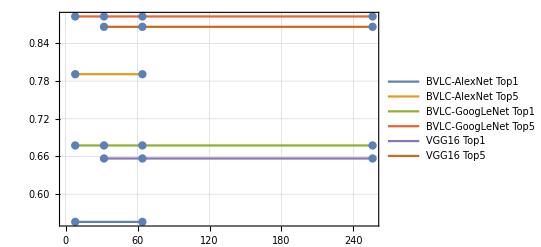

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

### Top1 / Top5 Model Accuracy on AMD64 & Minsky for MXNet

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

```mathematica
ListLinePlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Mesh->All,
PlotTheme->"Detailed"
]
```

-Graphics-

### Top1 / Top5 Model Accuracy on Minsky for Caffe2

```mathematica
models=GroupBy[$AccuracyInformation,Lookup["Model"]];
```

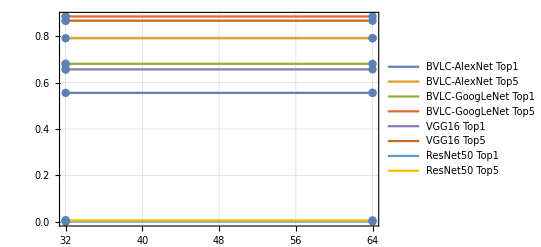

```mathematica
ListPlot[
Catenate[
KeyValueMap[
Function[{key,val},
{
Legended[Table[{e["BatchSize"],e["Top1"]},{e,val}],key <>" Top1"],
Legended[Table[{e["BatchSize"],e["Top5"]},{e,val}],key <>" Top5"]
}
],
models
]],
Joined->True,
Mesh->All,
PlotTheme->"Detailed"
]
```

```mathematica
BarChart[
Catenate[
KeyValueMap[
Function[{key,val},
Join[
Table[<|ToString[e["BatchSize"]] <> " Top1"->Callout[e["Top1"],key <> " Top1"]|>,{e,val}],
Table[<|ToString[e["BatchSize"]] <> " Top5"->Callout[e["Top5"],key <> " Top5"]|>,{e,val}]
]
],
models
]],
ChartLabels->{32,64},
ChartLegends->Automatic,
PlotTheme->"Detailed"
]
```

-Graphics-

```mathematica
Dataset[models]
```

Dataset[<>]

### Model Timing on Minsky for Caffe2

```mathematica
$DurationInformation;
```

```mathematica
Length[$DurationInformation]
```

24

```mathematica
models=GroupBy[$DurationInformation,Lookup["FrameworkModel"]];
```

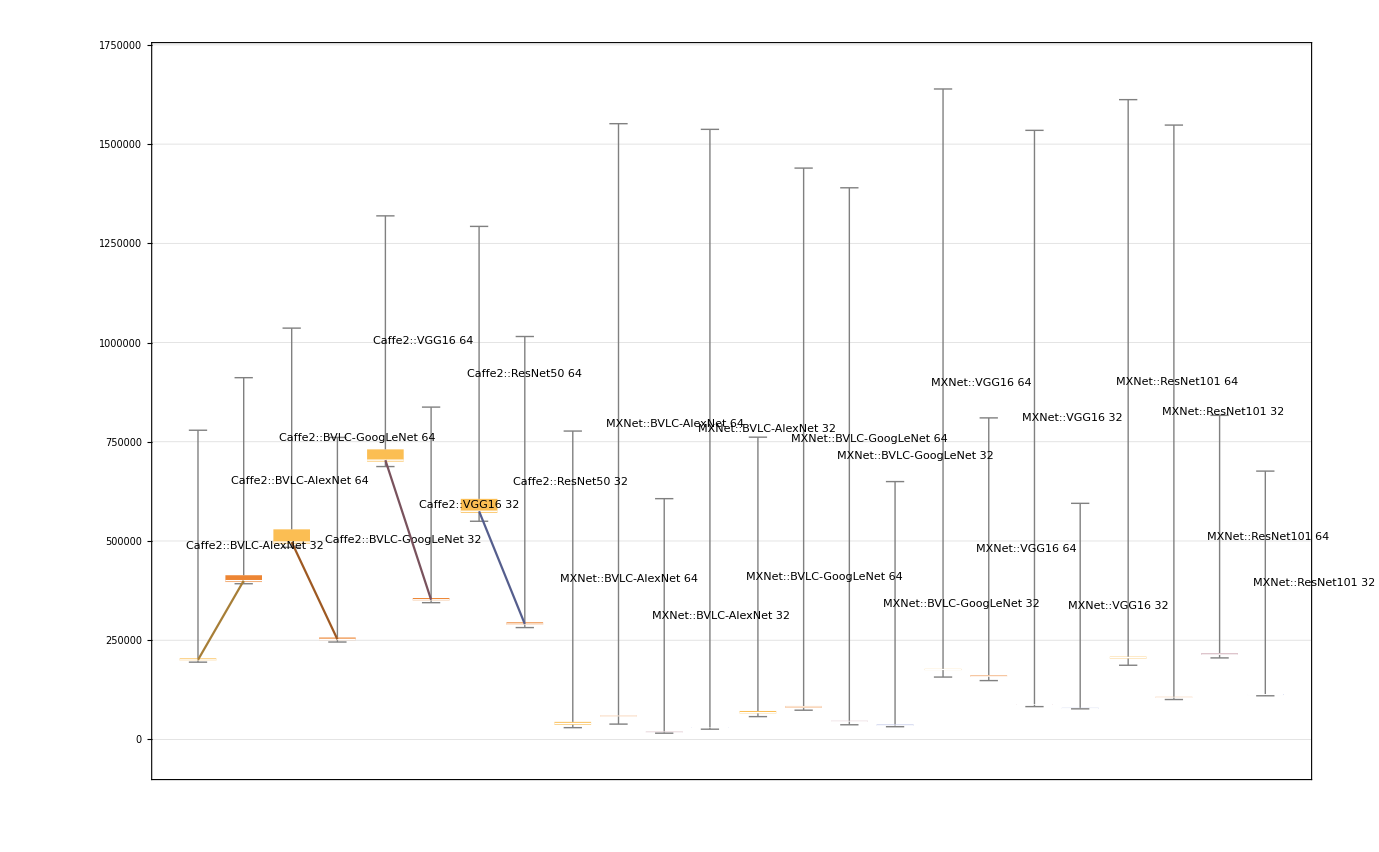

```mathematica
BoxWhiskerChart[
KeyValueMap[
Function[{key,val},
Table[
Labeled[e["Durations"],key <>" " <>ToString[e["BatchSize"]],Left,RotateLabel->True],
{e,val}
]
],
models
],
Joined->True,
LabelingFunction->Automatic,
PlotTheme->"Detailed"
]
```

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
Callout[{e["BatchSize"],Median[e["Durations"]]/e["BatchSize"]},
e["HostName"]<>"::"<>e["Framework"]<>"::"<>ToString[e["BatchSize"]]
],
{e,SortBy[val,#["BatchSize"]&]}
],
key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (us)"}
]
```

-Graphics-

```mathematica
ListPlot[
KeyValueMap[
Function[{key,val},
Legended[
Table[
duration=UnitConvert[Quantity[Median[e["Durations"]]/e["BatchSize"],"Microseconds"],"Milliseconds"];
Tooltip[
Callout[
{e["BatchSize"],duration},
e["HostName"]<>"::"<>e["Framework"]<>"::"<>ToString[e["BatchSize"]]
],
GeneralUtilities`Infobox[
<|
"HostName"->e["HostName"],
"MachineArchitecture"->e["MachineArchitecture"],
"UsingGPU"->e["UsingGPU"],
"Duration"->duration,
"BatchSize"->e["BatchSize"]
|>,
"Information"
]
],
{e,SortBy[val,#["BatchSize"]&]}
],
First[val]["Framework"]<> "/"<>key
]
],
models
],
Mesh->All,
Joined->False,
Axes->True,
PlotTheme->"Grid",
AxesLabel->{"BatchSize","Median Time (ms)"}
]
```

-Graphics-